# -Graphics-

# Time Series

## The Basics

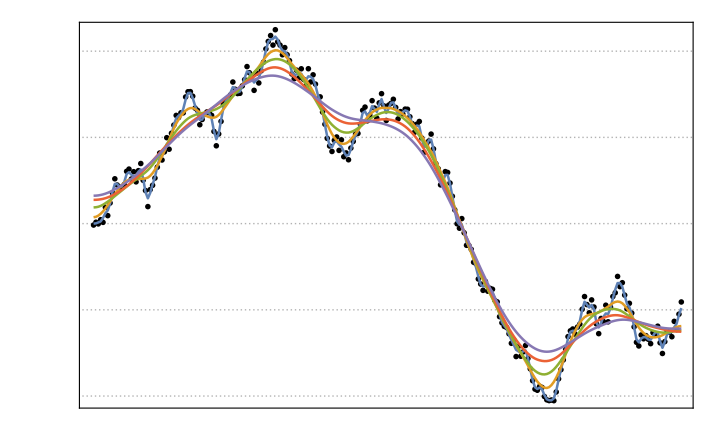

## Outline

### What Is a Time Series?

Definition of a times series

Times series in the Wolfram Language

TimeSeries

TemporalData

EventSeries

### Constructing Time Series

Lists of values and times

Dates

External data

Random processes

### Extracting Data from Time Series

TimeSeries properties

### Cleaning Time Series

Missing data

Irregular data

### Operations on Time Series

Direct arithmetic

TimeSeriesWindow

MovingMap

TimeSeriesResample

TimeSeriesMap

TimeSeriesThread

## What Is a Time Series?

Time series are tightly integrated into the Wolfram Language™, allowing for seamless workflows with absolute or calendar time, regular or irregular sampling, scalar or vector values, single or multiple series and in the presence of missing data. The Wolfram Language offers an extensive collection of tools for processing time series. These tools range from descriptive statistics, filters and visualisation to forecasts, simulation and highly automated modeling frameworks.

Guide: Time Series.

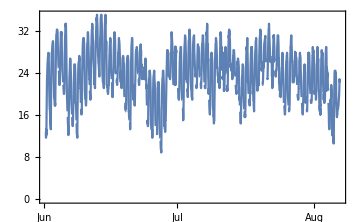
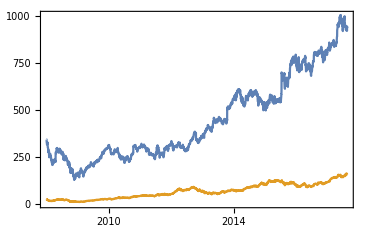
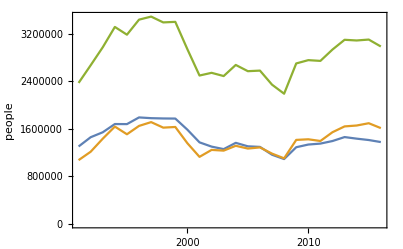

#### Definition

A time series is a series of time-stamped data points in chronological order.

#### Time series in the Wolfram Language

In the Wolfram Language, this time-stamped data is represented using three objects:

TimeSeries — assumes continuous-time observations and allows only one “path” (which could be univariate or multivariate of constant dimension). By default, the values between time stamps are interpolated linearly, but the interpolation method can be changed.

TemporalData — assumes continuous-time observations and allows more than one path (but the dimensionality of values for all paths must be consistent). By default, values between time stamps are “held from the left” (i.e. zero-order interpolation), but again the interpolation method can be changed.

EventSeries — assumes discrete-time events, so there is no interpolation between time stamps.

## Constructing Time Series

A TimeSeries object contains a single path of time-stamped values. It can be created in several different ways.

### Manual Construction

#### Lists of values and times

Create a TimeSeries from a list of values and a list of times:

```mathematica
values=RandomInteger[{1,10},10];
times={1,3,5,8,12,15,20,25,35,36};

timeSeries=TimeSeries[values,{times}];

ListLinePlot[timeSeries]
```

Note that the lists must be the same length.

#### A list of time-value pairs

Create a TimeSeries from a list of time-value pairs:

```mathematica
pairs=Transpose[{times, values}];

timeSeries=TimeSeries[pairs];

ListLinePlot[timeSeries]
```

#### Dates: specifying a starting point

Create a TimeSeries from a list of values and a starting date:

```mathematica
values=RandomInteger[{1, 20}, 10];

timeSeries1=TimeSeries[values,{{1982,5,24}}];
timeSeries2=TimeSeries[values,{"May 24 1982"}];

Map[
DateListPlot[#,]&,
{timeSeries1,timeSeries2}
]
```

Note that TimeSeries attempts to interpret dates written in natural language (ambiguous dates can be handled with DateFunction). Note also the visual differences between DateListPlot and ListLinePlot.

With no starting date provided, the times are assumed to be 1-second steps from 00:00:00 on 1st Jan 1900:

```mathematica
TimeSeries[values]["Dates"]
```

#### Dates: specifying start and end points

Create a TimeSeries from a list of values, a start date and an end date:

```mathematica
values=RandomInteger[{1, 20}, 10];
timeSeries=TimeSeries[values,{"2001", "2012"}];

DateListPlot[timeSeries, ]
```

Note that the values have been spread evenly over the time interval. These dates can be extracted and the differences between them checked:

```mathematica
timeSeries["DatePath"]
```

```mathematica
Differences[timeSeries["DatePath"][[All, 1]]]
```

### External Data

Get stock data for Google from 2005:

```mathematica
googleStocks=FinancialData["GOOGL",{2005}];
```

While typically external data would need to be cleaned and formatted, financial data is integrated into the Wolfram Language, so this stock data is already in time series form:

```mathematica
googleStocks[[1]]
```

Nevertheless, TimeSeries can be wrapped around the data to be sure:

```mathematica
gsTimeSeries=TimeSeries[googleStocks];

Map[
DateListPlot[#,  ]&,
{googleStocks, gsTimeSeries}
]
```

### Random Processes

Simulate time series data with a random process (in this case, a WienerProcess):

```mathematica
wienerData = TimeSeries[RandomFunction[WienerProcess[],{0,10,0.1}]]
```

```mathematica
ListLinePlot[wienerData,Filling->Axis,AxesOrigin->{0,0}]
```

## Extracting Data from Time Series

Once you have a TimeSeries object, various properties can be extracted.

Create a TimeSeries from a random process:

```mathematica
ouTimeSeries = TimeSeries[RandomFunction[OrnsteinUhlenbeckProcess[0,0.1,0.3,1],{0,20,0.1}]];
```

See its properties:

```mathematica
ouTimeSeries["Properties"]
```

See the specific values for these properties:

```mathematica
AssociationMap[
ouTimeSeries[#] &,
ouTimeSeries["Properties"]
]//Dataset
```

Plot the path (this gives the same result as plotting ouTimeSeries directly):

```mathematica
DateListPlot[ouTimeSeries["Path"]]
```

Plot the path using the interpolated path function:

```mathematica
Plot[
ouTimeSeries["PathFunction"][x],
{x, 0, 20}
]
```

### Exercise 1

In this exercise, you will obtain some temporal data from a file, clean it and obtain a TimeSeries object from it. The data consists of Wisconsin employment time series from January 1961 to October 1975 (Labor market, Hipel & McLeod, 1994).

a) Import the data from wisconsin-employment-time-series.csv into a Mathematica notebook and check its dimensions.
b) Remove any unnecessary rows or columns and check the data types.
c) Convert the date-like data to a DateObject.
d) Convert the data to a TimeSeries and save it to a variable (you will need it for later exercises).

## Cleaning Time Series

To obtain meaningful descriptive statistics from data, it needs to be in a computable form. In real-world time-stamped data, some data values may be missing or irregularly spaced.

### Missing Data

Construct a time series from temperature values using WeatherData:

```mathematica
temps=TimeSeries[WeatherData["Champaign","Temperature",{{2020, 1}, {2020, 2}}]];
```

Several temperature values are missing:

```mathematica
DateListPlot[temps]
```

Using MissingDataMethod in TimeSeries, the missing data values can be substituted for constants or interpolated (first-order interpolation is used by default).

Apply second-order interpolation to the data:

```mathematica
tempsNoMissing=TimeSeries[temps,MissingDataMethod->{"Interpolation",InterpolationOrder->2}]
```

Compare with the old data (hover your mouse over the plot):

```mathematica
Mouseover[
DateListPlot[temps, ImageSize -> 500],
DateListPlot[{tempsNoMissing, temps}, PlotStyle -> {RGBColor[0.880722, 0.611041, 0.142051], RGBColor[0.368417, 0.506779, 0.709798]}, ImageSize -> 500]
]
```

Get statistics from the new data:

```mathematica
Through[{Min,Max,Mean,Median}[tempsNoMissing]]
```

### Irregular Data

#### Regularising data

Get the log returns of the S&P 500 index from 2014 to 2018:

```mathematica
sp500Data=Log[1+TimeSeries[FinancialData["SP500","FractionalChange",{{2014,1,1},{2018,1,1}}]]]
```

```mathematica
DateListPlot[sp500Data, ]
```

The computation of CovarianceFunction requires a time series to be regularly sampled:

```mathematica
RegularlySampledQ[sp500Data]
```

```mathematica
CorrelationFunction[sp500Data,{10}]
```

The irregularity of the data can be accounted for in two ways. One option is to use the TemporalRegularity option in TimeSeries.

##### Method I: TemporalRegularity

Get the same data as before, but this time assume it is regular:

```mathematica
sp500DataRegular1=TimeSeries[sp500Data,TemporalRegularity->True]
```

The correlation function can now be calculated:

```mathematica
RegularlySampledQ[sp500DataRegular1]

corrFunct1=CorrelationFunction[sp500DataRegular1,{10}]
```

However, the data has not actually been regularised—merely it has been labelled that way to allow certain functions to be applied to it:

```mathematica
ListPlot[Differences[sp500DataRegular1["Dates"]]]
```

To truly regularise the data, you can sample from it at regular intervals with TimeSeriesResample.

##### Method II: TimeSeriesResample

Take daily samples from the data:

```mathematica
sp500DataRegular2=TimeSeriesResample[sp500Data,"Day"]
```

Again, the correlation function can now be calculated:

```mathematica
RegularlySampledQ[sp500DataRegular2]

corrFunct2=CorrelationFunction[sp500DataRegular2,{10}]
```

Compare the two correlation functions:

```mathematica
ListPlot[{corrFunct1, corrFunct2}, ]
```

This time, the data has actually been regularised:

```mathematica
ListPlot[Differences[sp500DataRegular2["Dates"]]]
```

#### Relative regularity

An important thing to note is that regularity is relative. TimeSeries data may be regular relative to calendar time, but not to absolute time.

Consider the following S&P 500 data from January 2014:

```mathematica
sp500Data = TimeSeries[…];
```

The data has several gaps including weekends and one federal holiday (Martin Luther King Jr. day):

```mathematica
DateListPlot[sp500Data,]
```

Despite this, the data is recognised as being regularly sampled:

```mathematica
RegularlySampledQ[sp500Data]
```

## Operations on Time Series

TimeSeries objects can be manipulated in many ways; as well as regular arithmetic, there exist special functions for computing with them. In this section, you will look at TimeSeriesWindow, TimeSeriesResample, TimeSeriesMap and TimeSeriesThread.

Get a list of all time series-related functions:

```mathematica
?System`*TimeSeries*
```

### Direct Arithmetic

Mathematical operations on TimeSeries will act on the values of each time-value pair.

#### Operating on a single time series

Create a time series starting at time t=1:

```mathematica
timeSeries=TimeSeries[{2,3,4,5},{1}];
```

Apply some arithmetic operations to the time series:

```mathematica
timeSeriesOperations = {
timeSeries,
timeSeries/2,
timeSeries-1,
Exp[-timeSeries/10]
}
```

Note that the operations are automatically mapped across the time series values.

Visualise the results:

```mathematica
ListLinePlot[
timeSeriesOperations,
PlotLegends->{"Original","1/2","−1","Exp"}
]
```

#### Combining multiple aligned time series

Create two time series:

```mathematica
timeSeries1=TimeSeries[{2,3,4,5, 6},{1}];
timeSeries2=TimeSeries[{-2,-1,0,1, 2},{1}];
```

Combine the time series in various ways:

```mathematica
timeSeriesOperations = {
timeSeries1+timeSeries2,
timeSeries1-timeSeries2,
timeSeries1*timeSeries2,
timeSeries1/timeSeries2
}
```

Visualise the results:

```mathematica
ListLinePlot[
timeSeriesOperations,
PlotLegends->{"Plus","Minus","Times","Divide"}
]
```

Note that the 1/0 value which produced an error has been dropped.

#### Combining multiple misaligned time series

Create two time series with misaligned time stamps:

```mathematica
timeSeries1=TimeSeries[{10,5,10},{{0,2,3.5}}];
timeSeries2=TimeSeries[{1,2,3,4},{1}];
```

Visualise the misalignment:

```mathematica
NumberLinePlot[{timeSeries1["Times"],timeSeries2["Times"]},PlotStyle->PointSize[0.03]]
```

Add the time series together and visualise the result (hover your mouse over the plot):

```mathematica
timeSeriesSum = timeSeries1 + timeSeries2;

Mouseover[
ListLinePlot[{timeSeries1, timeSeries2},],
ListLinePlot[{timeSeries1, timeSeries2, timeSeriesSum},]
]
```

Note that the resulting time series is defined only where the time ranges overlap (including interpolated sections).

### Time Series Windows

A window of a time series is just a section of it over a specified time interval. Windows can be extracted from TimeSeries objects with TimeSeriesWindow.

Get the daily maximum temperatures for Champaign, IL over the period of one year:

```mathematica
champaignYearlyTemps=TimeSeries[WeatherData["Champaign","MaxTemperature",{{2016,1,1},{2016,12,31},"Day"}]]
```

Visualise the temperature distribution throughout the year:

```mathematica
SmoothHistogram[TimeSeries[QuantityMagnitude[champaignYearlyTemps],MissingDataMethod->"Interpolation"], ]
```

Extract the summer temperatures from the time series:

```mathematica
champaignSummerTemps=TimeSeriesWindow[champaignYearlyTemps,{"Jun 21 2016","Sep 21 2016"}]
```

Plotting both time series together shows that summer weather is generally warmer and less variable:

```mathematica
SmoothHistogram[#,  ]&/@ {
TimeSeries[QuantityMagnitude[champaignYearlyTemps],MissingDataMethod->"Interpolation"],
TimeSeries[QuantityMagnitude[champaignSummerTemps],MissingDataMethod->"Interpolation"]
} // Show
```

### Moving Maps

A moving average of a list of data is a series of averages taken over sequential sub-sequences of the data, effectively “smoothing” it. This can be done with MovingAverage:

```mathematica
MovingAverage[{a,b,c,d,e},3]
```

MovingMap is a generalisation of MovingAverage that is particularly useful for time series data:

```mathematica
MovingMap[f,{a,b,c,d,e},Quantity[3,"Events"]]
```

Note that without the Quantity specification, MovingMap looks at the intervals between points (i.e. windows), not the points themselves:

```mathematica
MovingMap[f,{a,b,c,d,e},2]
```

#### Window size

The size of windows used in a moving map is highly customisable.

Get the daily temperatures for Champaign, IL over the winter period:

```mathematica
champaignWinterTemps=TimeSeries[WeatherData["Chicago","Temperature",{"Dec 2016","Feb 2017"}],MissingDataMethod->Automatic];
```

Take a moving median average over windows of at most one day:

```mathematica
dailyMedian1=MovingMap[Median,champaignWinterTemps,{{1,"Day"}}]
```

Take another moving median average over regular 4-hour windows:

```mathematica
dailyMedian2=MovingMap[Median,champaignWinterTemps,{{1,"Day"},Automatic,{4,"Hour"}}]
```

At first glance, the new time series look similar (hover your mouse over the plot):

```mathematica
Mouseover[
DateListPlot[{champaignWinterTemps, dailyMedian1},],
DateListPlot[{champaignWinterTemps, dailyMedian2}, ]
]
```

However, only the second set of data is regular:

```mathematica
Map[
ListPlot[#,]&,
{dailyMedian1, dailyMedian2}
]
```

#### Window alignment

Windows in a moving map can be aligned right (default), centre or left, relative to the time stamps in the data.

```mathematica
Map[
MovingMap[f,TimeSeries[Range[5]],{Quantity[3,"Events"], #}]&,
{Right, Center, Left}
]
```

Get stock data for Apple from 2000 to 2017:

```mathematica
appleStocks=TimeSeries[FinancialData["AAPL",{"2000","2017"}]];
```

Take three 6-month moving median averages with different alignments:

```mathematica
{appleMedian1, appleMedian2, appleMedian3}=Map[
MovingMap[Median,appleStocks,{Quantity[6,"Months"],#}]&,
{Right,Center,Left}
];
```

Visualise the moving averages:

```mathematica
Show[
DateListLogPlot[appleStocks, ],
DateListLogPlot[{appleMedian1, appleMedian2, appleMedian3}, ]
]
```

#### Custom functions

While it is typical to use a statistical average in MovingMap (such as Mean or Median), it can take arbitrary functions.

Get all data for the S&P 500 index:

```mathematica
sp500AllData = TimeSeries[FinancialData["SP500",All]]
```

Apply and visualise different moving map functions:

```mathematica
sp500StandardDeviation=MovingMap[StandardDeviation,sp500AllData,{5*365,"Day"}];
sp500InterquartileRange=MovingMap[InterquartileRange,sp500AllData,"Year"];
sp500Range=MovingMap[Max[#]-Min[#]&,sp500AllData,{2,"Year"}];
```

```mathematica
Map[
DateListPlot[#, Joined->True, Filling -> Axis]&,
{sp500AllData, sp500StandardDeviation, sp500InterquartileRange, sp500Range}
]
```

### Resampling

As seen earlier, irregularly sampled time series data can be regularised with TimeSeriesResample (or by using TemporalRegularity as an option in TimeSeries).

#### Business days

For financial data, it is often useful to resample it according to "BusinessDay".

Get closing values for Google from December 2016:

```mathematica
googleClosing=TimeSeries[FinancialData["GOOGL","Close",{{2016,12,1},{2016,12,31}}]]
```

This time series is not regularly sampled:

```mathematica
RegularlySampledQ[googleClosing]
```

Resample the data according to business day:

```mathematica
googleClosingRegular=TimeSeriesResample[googleClosing,"BusinessDay"]
```

(Note that what you consider to be a business day may depend on your region. The default HolidayCalendar is that of the United States, but you can set a calendar or location of your choice.)

The path has not changed, but the time series is now regularly sampled (relative to calendar time, at least):

```mathematica
SameQ[googleClosing["Path"], googleClosingRegular["Path"]]
```

```mathematica
RegularlySampledQ[googleClosingRegular]
```

#### Downsampling

When no specification is given, the default resampling setting is the value of MinimumTimeIncrement—the smallest interval between any two successive time stamps. However, you may wish to reduce the data by sampling less frequently—a process known as downsampling.

Get stock data for Caterpillar Inc. from 2015 to 2020:

```mathematica
catStocksDaily=TimeSeries[FinancialData["CAT",{"2015", "2020"}]];
```

There are lots of points in this dataset:

```mathematica
catStocksDaily["PathLength"]
```

Sample the data monthly to reduce the number of points:

```mathematica
catStocksMonthly=TimeSeriesResample[catStocksDaily,"Month"];

catStocksMonthly["PathLength"]
```

Visualise the path differences (hover your mouse over the plot):

```mathematica
Mouseover[
DateListPlot[catStocksDaily, ],
DateListPlot[catStocksMonthly, ]
]
```

### Mapping

A common financial calculation is to obtain the log returns of stocks and then find the underlying distribution. Getting the log returns can be done with TimeSeriesMap—the time series equivalent of Map.

##### Get log returns data

Get stock data for Apple from 2012:

```mathematica
appleStocks=TimeSeries[FinancialData["AAPL",{2012,1,1}]];

DateListPlot[appleStocks]
```

Use direct arithmetic to obtain the log returns of the ratios of the stock prices:

```mathematica
Log[Ratios[appleStocks]]
```

(Recall that arithmetic operations are mapped across TimeSeries data automatically.)

Get the same data with TimeSeriesMap in a more readable way:

```mathematica
appleLogReturns=TimeSeriesMap[Log,Ratios[appleStocks]]
```

Visualise the log returns:

```mathematica
DateListPlot[appleLogReturns]
```

##### Fit distributions to the data

Assuming that the data is distributed according to a normal or Tsallis q-Gaussian distribution, find parameters that best fit these distributions to the data:

```mathematica
estimatedNormalDist=EstimatedDistribution[Flatten[appleLogReturns["ValueList"]],NormalDistribution[μ,σ]]

estimatedTsallisQGaussianDist=EstimatedDistribution[Flatten[appleLogReturns["ValueList"]],TsallisQGaussianDistribution[μ,β,q]]
```

Visualise the distributions against the data:

```mathematica
Show[
Histogram[
QuantityMagnitude[appleLogReturns],
Automatic,
"PDF"
]
,
Plot[
Evaluate[{
PDF[estimatedNormalDist, x],
PDF[estimatedTsallisQGaussianDist, x]
}],
{x,-0.05,0.05},
PlotLegends->{"Normal","TsallisQGaussian","SmoothKernel"}
]
]
```

### Threading

TimeSeriesThread is the time series equivalent of MapThread.

##### Basic example

Thread two time series together using a function f:

```mathematica
ts1=TimeSeries[{Subscript[x, 1],Subscript[x, 2],Subscript[x, 3],Subscript[x, 4],Subscript[x, 5]},{1}];
ts2=TimeSeries[{Subscript[y, 1],Subscript[y, 2],Subscript[y, 3],Subscript[y, 4],Subscript[y, 5]},{1}];

TimeSeriesThread[f,{ts1,ts2}]["Path"]
```

##### A min-max envelope

TimeSeriesThread can be useful for computing “envelopes” for multiple time series paths.

Simulate 100 geometric Brownian motion processes:

```mathematica
geoBrownianMotion=RandomFunction[GeometricBrownianMotionProcess[0.0086,0.0217,26.88],{0,1,0.01},100];
```

TimeSeriesThread can be useful for calculating confidence intervals.

Compute the mean and standard deviation of the data over time:

```mathematica
μ=TimeSeriesThread[Mean,geoBrownianMotion];
σ=TimeSeriesThread[StandardDeviation,geoBrownianMotion];
```

Combine these to calculate a 95% confidence interval using the formula {μ(t)-1.95 σ(t), μ(t)+1.95 σ(t)}:

```mathematica
confidenceInterval=TimeSeriesThread[{#⟦1⟧-1.95#⟦2⟧,#⟦1⟧+1.95#⟦2⟧}&,{μ,σ}];
```

Visualise the result:

```mathematica
Show[
ListLinePlot[geoBrownianMotion,PlotStyle->Opacity[0.1]],
ListLinePlot[confidenceInterval,PlotStyle->Black]
]
```

### Exercise 2

In this exercise, you will explore how to customise resampling using TimeSeriesAggregate, essentially converting an irregular time series to a regular time series.

a) Using the Caterpillar Inc. data from the Downsampling section, apply TimeSeriesAggregate, holding the window to the right and taking the maximum value.
b) Check that the new time series is regularly sampled.
c) Plot the original time series and the new time series together.

## Summary

There are three types of time series object in the Wolfram Language (discrete paths, continuous paths, multiple paths).

Time series can be constructed in many ways (data lists, start and end dates, external data import, random processes).

Lots of information can be extracted from a TimeSeries object (dates, times, date path, path function, path length, …).

Time series can be modified to make later analysis easier (missing data points, irregular time steps).

Time series can be operated on in many ways (direct arithmetic, window extraction, moving averages, resampling, mapping, threading, …).